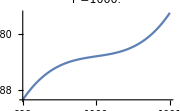
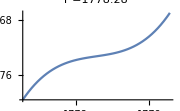
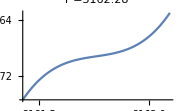
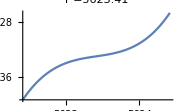
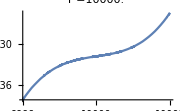
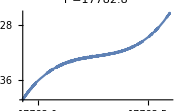
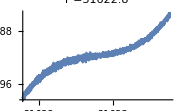
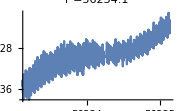

```mathematica
f[b_,r_]:=Module[{x,k2,Ek2,Kk2,δ,ck,ce,Δ},
δ=b-r;
Δ=δ/r;
x=1-Δ+Δ^2-Δ^3;
k2=((1/r-Δ)(1/r+Δ))/(4 (Δ+1));
(*
Ek2=EllipticE[k2];
Kk2=EllipticK[k2];
x=(r/b);
ce=(2 +14 x^2 );
ck=(1 +5 x +7 x^2 +3 x^3);
*)
ce=16-28Δ+42 Δ^2-56 Δ^3+42 Δ^4-28 Δ^5+14 Δ^6;
ck=16-28 Δ+44 Δ^2-63 Δ^3+57 Δ^4-50 Δ^5+37 Δ^6-18 Δ^7+9 Δ^8-3 Δ^9;
Ek2=EllipticE[k2];
Kk2=EllipticK[k2];

Ek2=π/2-π/8 k2;
Kk2=π/2+π/8 k2;

2 b^3 √x(ce Ek2-ck Kk2) ];

g[b_,r_]:=Module[{x=r/b,k2=((1-(b-r))(1+(b-r)))/(4 b r),Ek2,Kk2},
Ek2=EllipticE[k2];
Kk2=EllipticK[k2];

4b √x((-4+3x )Ek2+ 2Kk2)-3(√x)/(b x) Kk2 ];

Table[Plot[f[b,10^logr],{b,10^logr-1,10^logr+1},PlotLabel->StringJoin["r =",ToString[10^logr]],ImageSize->Small],{logr,3,5,0.25}]
```